```mathematica
f[x_]=x*Log[3,x]+x^2-5*x+2;
```

```mathematica
Plot[f[x],{x,0,5}]
```

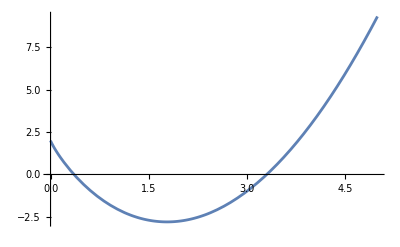

```mathematica
a=3;b=5;e=0.001;
(*a)метод Ньютона*)
```

```mathematica
x1=b;
Do[x2=x1;
	x1=(x1-f[x1]/f'[x1])//N;
		If[Abs[x2-x1]<e,
		Print["Решение x=",x2//N," получено за ", n ," шагов"];
Break[]],
{n,1,100}]
```

Решение x=3.3072 получено за 4 шагов

```mathematica
(*б)метод секущих*)
x1=b;
x0=b;
Do[x3=x1;
	x1=(x1-f[x1]*(x1-x0)/(f[x1]-f[x0]))//N;
		If[Abs[x3-x1]<e,
		Print["Решение x=",x3//N," получено за ", n ," шагов"];
Break[]],
{n,1,100}]
```

Решение x=3.3072 получено за 5 шагов